```mathematica
(* Import Paclets *)
Needs["NDSolve`FEM`"]
Needs["FEMAddOns`"]
```

E205

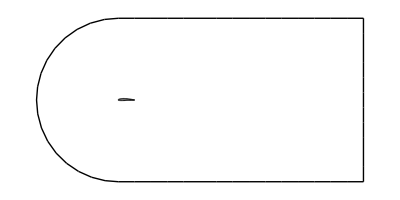

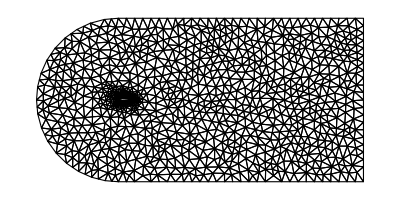

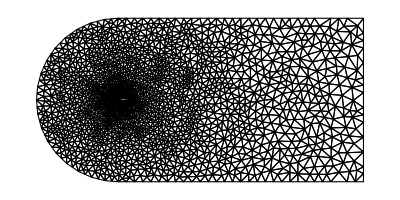

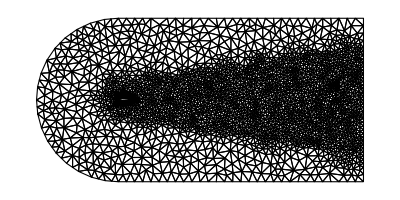

```mathematica
(* Mesh-Generation *)
(* choose the airfoil .dat file *)
airfoilDATA=Import["/Users/gustavomanzari/GitHub/Numerical-Simulation-for-NACA-Airfoil-with-Spalart-Allmaras-Turbulence-Model/Airfoil Data/e205.dat"];

airfoilClass=StringTemplate["`a``b`"][<|"a"->airfoilDATA[[1,1]],"b"->airfoilDATA[[1,2]]|>]
fnew[AirfoilClassString_]:=Table[
Symbol[AirfoilClassString<>t],
{t,{"Coords","Polygon"}}];
dataArray=fnew[airfoilClass];
dataArray[[1]]=airfoilDATA[[2;;-1]];
dataArray[[2]]=Polygon[dataArray[[1]]];
(* choose domain-size (1-length = 1-cord-length) *)
H=10; (* Domain height in cord-lengths *)
L=2*H;(* Domain Depth in cord-lengths *)
ℓ=H/5; (* Refining region core dimension in cord-lengths *)
B=(2H)/3;
Clear[x,𝓍];
𝓍rule=Solve[ℓ/(L-H/2+𝓍)==B/𝓍,𝓍];
𝓍=Abs[𝓍/.𝓍rule[[1]]];
bmesh1=ToBoundaryMesh[RegionUnion[Disk[{0,0},H/2],Rectangle[{0,-H/2},{L-H/2,H/2}]]];
bmesh2=ToBoundaryMesh[dataArray[[2]]];
Ω=BoundaryElementMeshDifference[bmesh1,bmesh2];
Ω["Wireframe"]
(* choose mesh-refining function *)
meshrefine[vertices_,area_]:=area>2/H;
f=Function[{vertices,area},area>1/(2.5 H^2) (0.1+5 Norm[Mean[vertices]])];
pred=(x^2+y^2≤(ℓ/2)^2||x≥0&&-((ℓ-B)/(H-2L))x-y≤ℓ/2&&((ℓ-B)/(H-2L))x-y≥-ℓ/2&&x≤L-H/2);
g=Function[{vertices,area},Block[{x,y},{x,y}=Mean[vertices];If[pred,area>1/(3*H),area>2/H]]];
ToElementMesh[Ω,MeshQualityGoal->"Maximal",MeshRefinementFunction->meshrefine]["Wireframe"]
ToElementMesh[Ω,MeshQualityGoal->"Maximal",MeshRefinementFunction->f]["Wireframe"]
ToElementMesh[Ω,MeshQualityGoal->"Maximal",MeshRefinementFunction->g]["Wireframe"]
```